```mathematica
(* materials: https://github.com/JarekDuda/SGD-OGR-Hessian-estimator/ *)
```

```mathematica
(* basic step in d dimensional subspace, using ng: noisy gradient in θ *)
sstep[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);     (* means *)
V=Orthogonalize[Table[v+Γ*ng,{v,V}]];   (* explore new directions*)
pθ=V.(θ-mθ);pg=V.(ng-mg);       (* mean subtractions & projections *)
θ-=α(m-m.Transpose[V].V);       (* momentum in remaining  directions *)                                                       
mθθ+=β(KroneckerProduct[pθ,pθ]-mθθ); {e,ev}=Eigensystem[mθθ];
mgθ+=β(KroneckerProduct[pg,pθ]-mgθ); evt=Transpose[ev];
pH=evt.((ev.s[mgθ].evt)/s[Table[e,d]]).ev;   (* Hessian estimator *) 
θ-=(ma[pH].(V.m)).V);      (* 1/|~eigenvalues of pH| in local subspace *)
eh[lm_]:=1/Map[Max[#,cut]&,Abs[lm]*div]; (* eigenvalue inv, div&cut *)
ma[A_]:=({e,ev}=Eigensystem[A];Transpose[ev].DiagonalMatrix[eh[e]].ev);

b=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x*y^3)^2;(* Beale function *)
f=Simplify[b+(b/.x->z)];v={x,y,z};𝔇=Length[v];(*3D:b(x,y)+b(z,y)*)
sub[p_]:=Table[v[[i]]->p[[i]],{i,𝔇}]; s[M_]:=M+Transpose[M];
g=Grad[f,v];H=Table[D[f,v1,v2],{v1,v},{v2,v}]; (*gradient,Hessian *)
noise:=RandomReal[NormalDistribution[0,ϵ],𝔇];ϵ=0.1;   (*Gaussian noise*)
α=0.001;β=0.6;γ=0.6;div=1.5;Γ=0.25;cut=10;      (* hyperparameters *) 
d=2;   V=RandomReal[0.001,{d,𝔇}];       (* dimension, basis of subspace *)
m=mg=mθ=Table[0.,𝔇]; θ={0,0,0};                                (* starting position *)
mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];steps=50;
Do[sstep[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
f/.sub[θ]
```

0.00119213

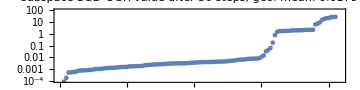

```mathematica
fv={};α=0.0000;β=0.6;γ=0.6;div=1.5;Γ=0.25;cut=10; steps=50;d=2; (* d=2 dim. subspace *)
paths=Table[m=mg=mθ=Table[0.,𝔇];θh={}; θ={sx,sy,sz};  (*starting position *)
   V=RandomReal[0.001,{d,𝔇}];   mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];
Do[AppendTo[θh,θ];sstep[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-2,2},{sy,-2,2},{sz,-2,2}];
plo=ListLogPlot[Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"subspace SGD-OGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

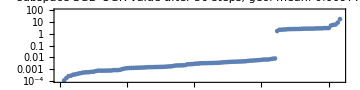

```mathematica
fv={};α=0;β=0.6;γ=0.6;div=1.5;Γ=0.25;cut=10; steps=50;d=1;  (* d=2 dim. subspace *)
paths=Table[m=mg=mθ=Table[0.,𝔇];θh={}; θ={sx,sy,sz};  (*starting position *)
   V=RandomReal[0.001,{d,𝔇}];   mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];
Do[AppendTo[θh,θ];sstep[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-2,2},{sy,-2,2},{sz,-2,2}];
plo=ListLogPlot[Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"subspace SGD-OGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

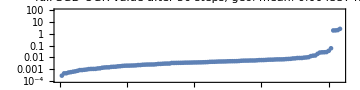

```mathematica
(* basic step using g: noisy gradient in θ *)
step[ng_]:=(m+=γ(ng-m);                                  (* update momentum, averages: *)
mθ+=β(θ-mθ);mθθ+=β(KroneckerProduct[θ-mθ,θ-mθ]-mθθ);
mg+=β(ng-mg);mgθ+=β(KroneckerProduct[ng-mg,θ-mθ]-mgθ);
mgθs=mgθ+Transpose[mgθ];{e,ev}=Eigensystem[mθθ];
pH=Transpose[ev].((ev.mgθs.Transpose[ev])/
(Table[e,d]+Transpose[Table[e,d]])).ev;      (* Hessian estimator *) 
θ-=ma[pH].m);                        (* 1/|~eigenvalues of pH: predicted Hessian| *)
eh[lm_]:=1/Map[Max[#,cut]&,Abs[lm]*div];   (* eigenvalue inv, div&cut *)
ma[A_]:=({e,ev}=Eigensystem[A];Transpose[ev].DiagonalMatrix[eh[e]].ev);

fv={};β=0.5;γ=0.6;div=1.5;cut=10; steps=50;d=3;
paths=Table[m=mg=mθ=Table[0.,d];θh={}; θ={sx,sy,sz};  (*starting position *)
mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];
Do[AppendTo[θh,θ];step[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-2,2},{sy,-2,2},{sz,-2,2}];
plo=ListLogPlot[Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"full SGD-OGR value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

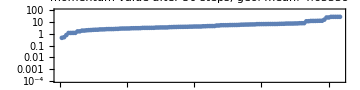

```mathematica
(* comparison with momentum method  *)
fv={};γ=0.5;α=0.004; steps=50;         (* momentum , for α=0.005  one escapes to infinity *)
stepmom[ng_]:=(m+=γ(ng-m);θ-=α*m);                 
paths=Table[m=Table[0.,d];θh={}; θ={sx,sy,sz}; (*starting position *)
Do[AppendTo[θh,θ];stepmom[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-2,2},{sy,-2,2},{sz,-2,2}];
plm=ListLogPlot[Sort[fv],PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"momentum value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

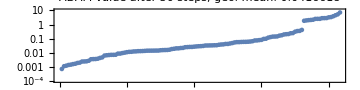

```mathematica
fv={};α=0.6;β1=0.8;β2=0.9;epsilon=10^-8.; steps=50;                 (* ADAM, tuned hyperparameters *)
stepADAM[ng_]:=(t++;m=β1*m+(1-β1)ng;vv=β2*vv+(1-β2)ng^2;
θ-=α*m/((epsilon+Sqrt[vv/(1-β2^t)])*(1-β1^t)));                 (* ADAM: https://arxiv.org/pdf/1412.6980  *)
paths=Table[m=Table[0.,d];θh={};vv=0;t=0; θ={sx,sy,sz}; (*starting position *)
Do[AppendTo[θh,θ];stepADAM[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-2,2},{sy,-2,2},{sz,-2,2}];
plm=ListLogPlot[Sort[fv],PlotRange->{0.0001,10},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"ADAM value after ",steps," steps, geo. mean: ",Exp[Mean[Log[fv]]]}]]
```

```mathematica
Row[{Table[path=paths[[3,i,j,1;;-1,1;;3]];mnmx=Map[MinMax,Transpose[path]];
Graphics3D[{Thickness[0.03],Line[path,VertexColors->Map[Hue,Range[steps]/steps/2]]}],{i,1,5},{j,1,5}]//Grid,Column[{"step",Grid[Transpose[{Range[steps],Map[Hue,Range[steps]/steps/2]}],Spacings->{0,-0.1}]}]}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-step
1 | Hue[Rational[1, 100]]
2 | Hue[Rational[1, 50]]
3 | Hue[Rational[3, 100]]
4 | Hue[Rational[1, 25]]
5 | Hue[Rational[1, 20]]
6 | Hue[Rational[3, 50]]
7 | Hue[Rational[7, 100]]
8 | Hue[Rational[2, 25]]
9 | Hue[Rational[9, 100]]
10 | Hue[Rational[1, 10]]
11 | Hue[Rational[11, 100]]
12 | Hue[Rational[3, 25]]
13 | Hue[Rational[13, 100]]
14 | Hue[Rational[7, 50]]
15 | Hue[Rational[3, 20]]
16 | Hue[Rational[4, 25]]
17 | Hue[Rational[17, 100]]
18 | Hue[Rational[9, 50]]
19 | Hue[Rational[19, 100]]
20 | Hue[Rational[1, 5]]
21 | Hue[Rational[21, 100]]
22 | Hue[Rational[11, 50]]
23 | Hue[Rational[23, 100]]
24 | Hue[Rational[6, 25]]
25 | Hue[Rational[1, 4]]
26 | Hue[Rational[13, 50]]
27 | Hue[Rational[27, 100]]
28 | Hue[Rational[7, 25]]
29 | Hue[Rational[29, 100]]
30 | Hue[Rational[3, 10]]
31 | Hue[Rational[31, 100]]
32 | Hue[Rational[8, 25]]
33 | Hue[Rational[33, 100]]
34 | Hue[Rational[17, 50]]
35 | Hue[Rational[7, 20]]
36 | Hue[Rational[9, 25]]
37 | Hue[Rational[37, 100]]
38 | Hue[Rational[19, 50]]
39 | Hue[Rational[39, 100]]
40 | Hue[Rational[2, 5]]
41 | Hue[Rational[41, 100]]
42 | Hue[Rational[21, 50]]
43 | Hue[Rational[43, 100]]
44 | Hue[Rational[11, 25]]
45 | Hue[Rational[9, 20]]
46 | Hue[Rational[23, 50]]
47 | Hue[Rational[47, 100]]
48 | Hue[Rational[12, 25]]
49 | Hue[Rational[49, 100]]
50 | Hue[Rational[1, 2]]